```mathematica
(* 2015/12/08 Toshiaki Matsushima *)
```

```mathematica
Color[i_,c_]:=Module[{x,r,g,b},x=i/(c+1);r=Max[0,Min[1,3-6x],3x-2];g=Max[0,Min[1,3x,2.5-3x]];b=Max[0,Min[1,6x-3,6-6x]];RGBColor[r,g,b]]
```

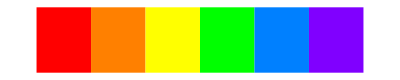

```mathematica
j=5;
Graphics[Table[{Color[i,j],Polygon[{{i,0},{i+1,0},{i+1,1},{i,1}}]},{i,0,j}]]
```

```mathematica
Tiling[h_,v_]:=Module[{n,m,c,TriT,TriB,TriL,TriR},
n=Length[h]-1;(*縦の長さ*)
m=Length[Flatten[h]]/Length[h];(*横の長さ*)
c=Max[Join[h,v]];(*色の数値の最大値*)
TriT[s_,t_]:={Color[h[[s]][[t]],c],Polygon[{{2t-2,2-2s},{2t,2-2s},{2t-1,1-2s}}]};(*上辺の三角形*)
TriB[s_,t_]:={Color[h[[s+1]][[t]],c],Polygon[{{2t-2,-2s},{2t,-2s},{2t-1,1-2s}}]};(*下辺の三角形*)
TriL[s_,t_]:={Color[v[[s]][[t]],c],Polygon[{{2t-2,-2s},{2t-2,2-2s},{2t-1,1-2s}}]};(*左辺の三角形*)
TriR[s_,t_]:={Color[v[[s]][[t+1]],c],Polygon[{{2t,-2s},{2t,2-2s},{2t-1,1-2s}}]};(*左辺の三角形*)
Graphics[{EdgeForm[Thick],Table[Table[{TriT[s,t],TriB[s,t],TriL[s,t],TriR[s,t]},{t,m}],{s,n}]}]]
```

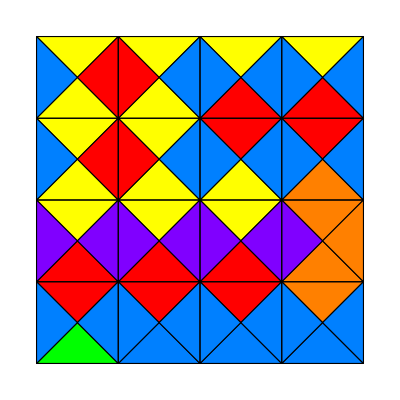

```mathematica
Tiling[{{2,2,2,2},{2,2,0,0},{2,2,2,1},{0,0,0,1},{3,4,4,4}},{{4,0,4,4,4},{4,0,4,4,4},{5,5,5,5,1},{4,4,4,4,4}}]
```

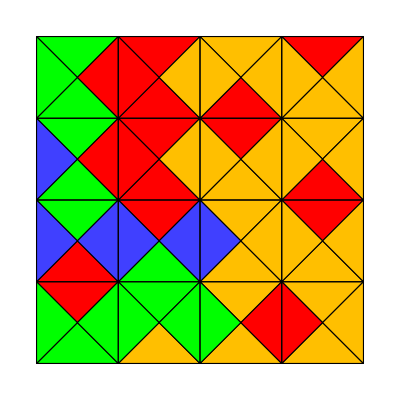

```mathematica
Tiling[{{2,0,1,0},{2,0,0,1},{2,0,1,0},{0,2,1,1},{2,1,1,1}},{{2,0,1,1,1},{3,0,1,1,1},{3,3,3,1,1},{2,2,2,0,1}}]
```

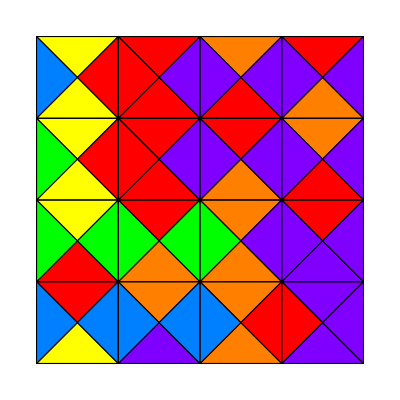

```mathematica
Tiling[{{2,0,1,0},{2,0,0,1},{2,0,1,0},{0,1,1,5},{2,5,1,5}},{{4,0,5,5,5},{3,0,5,5,5},{3,3,3,5,5},{4,4,4,0,5}}]
```

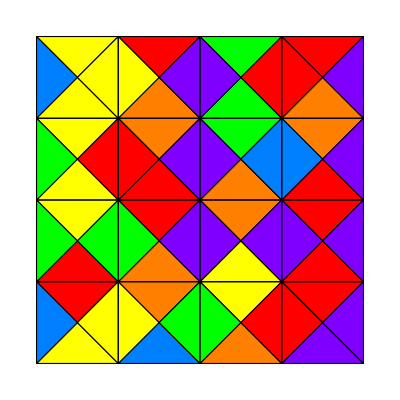

```mathematica
Tiling[{{2,0,3,0},{2,1,3,1},{2,0,1,0},{0,1,2,0},{2,4,1,5}},{{4,2,5,0,5},{3,0,5,4,5},{3,3,5,5,5},{4,2,3,0,5}}]
```

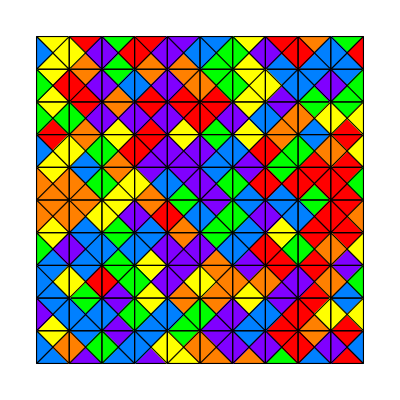

```mathematica
Tiling[{{2,0,3,0,5,4,2,0,1,3},{2,1,3,1,1,3,2,4,4,4},{2,0,1,0,0,0,2,5,3,3},{0,1,2,0,2,3,2,1,4,0},{2,4,1,5,5,4,5,3,0,0},{1,1,2,1,3,5,4,4,3,0},{2,4,3,4,1,3,4,2,0,0},{4,4,3,2,5,1,5,0,0,5},{4,3,5,2,1,1,2,5,0,4},{2,4,5,4,3,5,4,0,1,0},{4,5,4,5,2,1,1,3,4,0}},{{4,2,5,0,5,4,3,5,0,4,0},{3,0,5,4,5,1,3,2,4,5,3},{3,3,5,5,5,0,5,4,1,2,2},{4,2,3,0,5,5,4,0,3,1,2},{1,1,3,2,4,5,3,0,0,0,3},{1,1,2,5,0,4,3,5,4,0,1},{3,5,4,4,5,5,4,0,3,1,2},{4,2,0,3,5,2,1,1,5,1,3},{5,4,4,3,4,3,5,4,0,2,2},{4,1,3,4,2,1,5,5,0,5,4}}]
```

```mathematica
(*論文画像用,ズーム300%でスクリーンショット*)
```

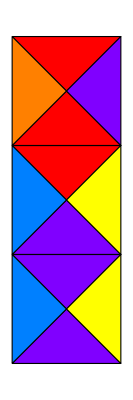
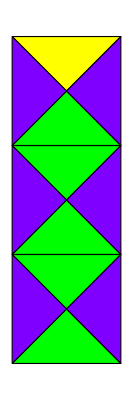
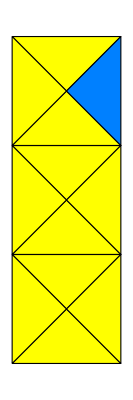
{-Graphics-,1,-Graphics-,1,-Graphics-}

```mathematica
{Tiling[{{0},{0},{5},{5}},{{1,5},{4,2},{4,2}}],1,Tiling[{{2},{3},{3},{3}},{{5,5},{5,5},{5,5}}],1,Tiling[{{1},{1},{1},{1}},{{1,2},{1,1},{1,1}}]}
```

```mathematica
(*論文画像用,ズーム200%でスクリーンショット*)
```

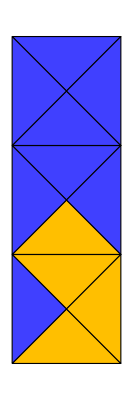
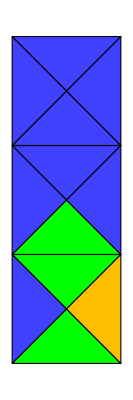
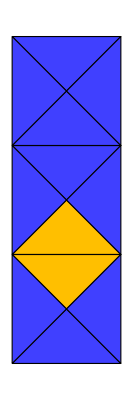
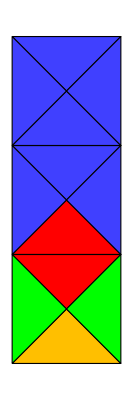
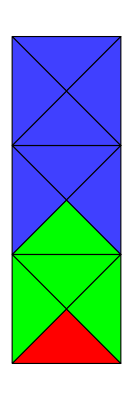
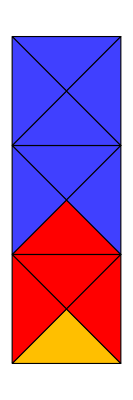
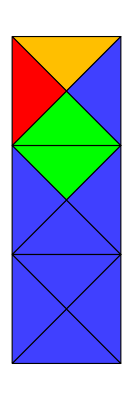
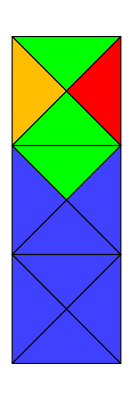
{{-Graphics-,1,-Graphics-,1,-Graphics-,1,-Graphics-,1,-Graphics-,1,-Graphics-},111,1,{-Graphics-,1,-Graphics-,1,-Graphics-,1,-Graphics-,1,-Graphics-}}

```mathematica
{{Tiling[{{3},{3},{1},{1}},{{3,3},{3,3},{3,1}}],1,Tiling[{{3},{3},{2},{2}},{{3,3},{3,3},{3,1}}],1,Tiling[{{3},{3},{1},{3}},{{3,3},{3,3},{3,3}}],1,Tiling[{{3},{3},{0},{1}},{{3,3},{3,3},{2,2}}],1,Tiling[{{3},{3},{2},{0}},{{3,3},{3,3},{2,2}}],1,Tiling[{{3},{3},{0},{1}},{{3,3},{3,3},{0,0}}]},111,1,{Tiling[{{1},{2},{3},{3}},{{0,3},{3,3},{3,3}}],1,Tiling[{{2},{2},{3},{3}},{{1,0},{3,3},{3,3}}],1,Tiling[{{2},{0},{3},{3}},{{1,1},{3,3},{3,3}}],1,Tiling[{{3},{2},{3},{3}},{{1,3},{3,3},{3,3}}],1,Tiling[{{1},{1},{3},{3}},{{3,0},{3,3},{3,3}}]}}
```

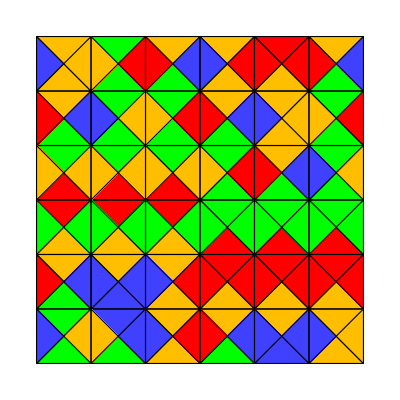

```mathematica
Tiling[{{1,2,1,1,0,1},{1,2,2,1,1,2},{2,2,2,2,1,2},{0,0,0,2,2,2},{1,1,1,0,0,0},{2,3,1,1,1,1},{2,2,1,2,3,1}},{{3,1,0,3,0,0,3},{0,3,1,0,3,1,0},{1,1,1,1,0,3,1},{2,2,2,2,2,2,2},{0,3,3,0,0,0,0},{3,1,3,0,3,3,1}}]
```

```mathematica
(*モノクロ版も試作*)
```

```mathematica
Color2[i_,c_]:=Module[{x},x=i/(c+1);RGBColor[x,x,x]]
```

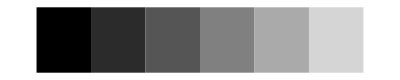

```mathematica
j=5;
Graphics[Table[{Color2[i,j],Polygon[{{i,0},{i+1,0},{i+1,1},{i,1}}]},{i,0,j}]]
```

```mathematica
Tiling2[h_,v_]:=Module[{n,m,c,TriT,TriB,TriL,TriR},
n=Length[h]-1;(*縦の長さ*)
m=Length[Flatten[h]]/Length[h];(*横の長さ*)
c=Max[Join[h,v]];(*色の数値の最大値*)
TriT[s_,t_]:={Color2[h[[s]][[t]],c],Polygon[{{2t-2,2-2s},{2t,2-2s},{2t-1,1-2s}}]};(*上辺の三角形*)
TriB[s_,t_]:={Color2[h[[s+1]][[t]],c],Polygon[{{2t-2,-2s},{2t,-2s},{2t-1,1-2s}}]};(*下辺の三角形*)
TriL[s_,t_]:={Color2[v[[s]][[t]],c],Polygon[{{2t-2,-2s},{2t-2,2-2s},{2t-1,1-2s}}]};(*左辺の三角形*)
TriR[s_,t_]:={Color2[v[[s]][[t+1]],c],Polygon[{{2t,-2s},{2t,2-2s},{2t-1,1-2s}}]};(*左辺の三角形*)
Graphics[{EdgeForm[Thick],Table[Table[{TriT[s,t],TriB[s,t],TriL[s,t],TriR[s,t]},{t,m}],{s,n}]}]]
```

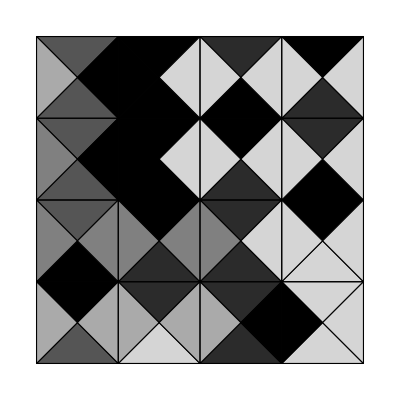

```mathematica
Tiling2[{{2,0,1,0},{2,0,0,1},{2,0,1,0},{0,1,1,5},{2,5,1,5}},{{4,0,5,5,5},{3,0,5,5,5},{3,3,3,5,5},{4,4,4,0,5}}]
```

```mathematica
(*グレースケール版も試作*)
```

```mathematica
Color3[i_,c_]:=Module[{x,r,g,b,x2},x=i/(c+1);r=Max[0,Min[1,3-6x],3x-2];g=Max[0,Min[1,3x,2.5-3x]];b=Max[0,Min[1,6x-3,6-6x]];
x2=0.3*r+0.6*g+0.1*b;RGBColor[x2,x2,x2]]
```

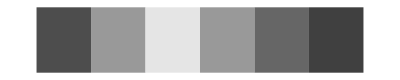

```mathematica
j=5;
Graphics[Table[{Color3[i,j],Polygon[{{i,0},{i+1,0},{i+1,1},{i,1}}]},{i,0,j}]]
```

```mathematica
Tiling3[h_,v_]:=Module[{n,m,c,TriT,TriB,TriL,TriR},
n=Length[h]-1;(*縦の長さ*)
m=Length[Flatten[h]]/Length[h];(*横の長さ*)
c=Max[Join[h,v]];(*色の数値の最大値*)
TriT[s_,t_]:={Color3[h[[s]][[t]],c],Polygon[{{2t-2,2-2s},{2t,2-2s},{2t-1,1-2s}}]};(*上辺の三角形*)
TriB[s_,t_]:={Color3[h[[s+1]][[t]],c],Polygon[{{2t-2,-2s},{2t,-2s},{2t-1,1-2s}}]};(*下辺の三角形*)
TriL[s_,t_]:={Color3[v[[s]][[t]],c],Polygon[{{2t-2,-2s},{2t-2,2-2s},{2t-1,1-2s}}]};(*左辺の三角形*)
TriR[s_,t_]:={Color3[v[[s]][[t+1]],c],Polygon[{{2t,-2s},{2t,2-2s},{2t-1,1-2s}}]};(*左辺の三角形*)
Graphics[{EdgeForm[Thick],Table[Table[{TriT[s,t],TriB[s,t],TriL[s,t],TriR[s,t]},{t,m}],{s,n}]}]]
```

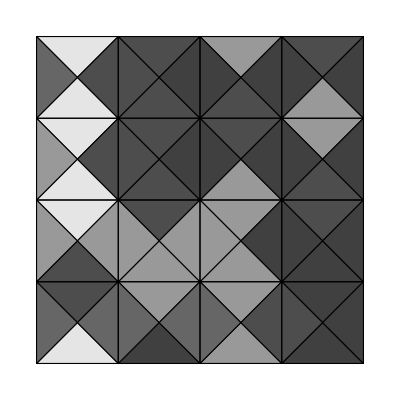

```mathematica
Tiling3[{{2,0,1,0},{2,0,0,1},{2,0,1,0},{0,1,1,5},{2,5,1,5}},{{4,0,5,5,5},{3,0,5,5,5},{3,3,3,5,5},{4,4,4,0,5}}]
```